```mathematica
fixLegend[size_][legend_]:=ReplaceAll[legend,{g_Graphics:>Show[g,ImageSize->Automatic->{Automatic,size},BaselinePosition->Axis],Pane->Function@#}]
MakeBoxes[stripGridAlignment[expr_],form_]^:=ReplaceAll[MakeBoxes[expr,form],Rule[GridBoxAlignment,_]->Sequence[]]
```

```mathematica
Compute v, σ,tmrca tables
```

Syntax::tsntxi: "Computev,σ,tmrcatables" is incomplete; more input is needed.

```mathematica
Nh=10^9;

Dmin = 2*10^-4;
Dmax = 10^-2; (*usually 10^-2*)
Dchange = (Dmax-Dmin)/21.;
Dvals = Table[DD, {DD,Dmin,Dmax,Dchange}];
```

```mathematica
stable = Table[1/bstar,{bstar,0.5,20,.1}];
```

```mathematica
solutions=Table[NSolve[{v==NI/(Nh*stable[[i]]),v==Dvals[[Dind]]^(2/3)*stable[[i]]^(1/3)*(24*Log[NI*(Dvals[[Dind]]*stable[[i]]^2)^(1/3)])^(1/3)},{v,NI},Reals],{i,1,Length[stable]},{Dind, 1, Length[Dvals]}];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

```mathematica
vtable1 = Table[{Dvals[[Dind]],v/.solutions[[i]][[Dind]][[1]]},{i,1,Length[stable]},{Dind, 1, Length[Dvals], 1 }];
NItable1 = Table[{Dvals[[Dind]],NI/.solutions[[i]][[Dind]][[1]]},{i,1,Length[stable]},{Dind,1 ,Length[Dvals], 1}];

vtable2 = Table[{Dvals[[Dind]],v/.solutions[[i]][[Dind]][[2]]},{i,1,Length[stable]},{Dind, 1, Length[Dvals], 1 }];
NItable2 = Table[{Dvals[[Dind]],NI/.solutions[[i]][[Dind]][[2]]},{i,1,Length[stable]},{Dind,1 ,Length[Dvals], 1}];
```

```mathematica
sigpoints1 = Table[{stable[[sind]],((vtable1[[sind]][[Dind]][[2]])/stable[[sind]])^(1/2)},{sind,1,Length[stable]},{Dind, 1, Length[Dvals]}];
sigpoints2 = Table[{stable[[sind]],((vtable2[[sind]][[Dind]][[2]])/stable[[sind]])^(1/2)},{sind,1,Length[stable]},{Dind, 1, Length[Dvals]}];

α=1.66;
tmrcapoints1 = Table[{stable[[sind]],(α*(sigpoints1[[sind]][[Dind]][[2]])^2)/(2*Dvals[[Dind]])},{sind,1,Length[stable]},{Dind, 1, Length[Dvals]}];
tmrcapoints2 = Table[{stable[[sind]],(α*(sigpoints2[[sind]][[Dind]][[2]])^2)/(2*Dvals[[Dind]])},{sind,1,Length[stable]},{Dind, 1, Length[Dvals]}];
```

## v plots

For nontrivial solution to equations

```mathematica
vtable=vtable2 ;
```

```mathematica
1. increasing as a function of s
```

1. a as function increasing of s

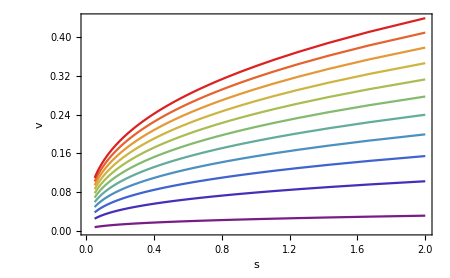

```mathematica
vpoints = Table[{stable[[sind]],vtable[[sind]][[Dind]][[2]]},{sind,1,Length[stable]},{Dind, 1, Length[Dvals],2}];
unjoinedvplot = ListPlot[Transpose[vpoints], Joined->False, AxesLabel->{"s","v"}, PlotRange->All];
joinedvplot = ListPlot[Transpose[vpoints], 
Joined->True, 
FrameLabel->{"s","v",None,None}, 
PlotRange->All, 
Frame->{True,True,False,False},
FrameStyle->{Black},
LabelStyle->{FontSize->24,Black},
PlotStyle->ColorData["Rainbow"][[1]],
ImageSize->450]
```

```mathematica
2. heatmap of max v
```

```mathematica
bvals=Table[1/stable[[sind]],{sind,1,Length[stable]}];
```

```mathematica
b/(cos SuperStar[θ]) on x axis
```

```mathematica
vmaxtab = Table[{1/stable[[sind]],vtable[[sind]][[Dind]][[2]]},{sind,1,Length[stable]},{Dind, 1, Length[Dvals],1}];
```

```mathematica
vpoints2= Table[{bvals[[i]],Dvals[[Dind]],v/.solutions[[i]][[Dind]][[2]]},{i,1,Length[stable]},{Dind, 1, Length[Dvals], 1 }];
Flatten[vpoints2,1];
Dimensions[vpoints2]
```

{196,22,3}

```mathematica
Dvals[[22]]
```

0.01

```mathematica
ListPlot[Table[{vpoints2[[i,d,1]],vpoints2[[i,d,3]]},{d,20,Length[Dvals]},{i,1,Length[stable]}],Joined->False];
```

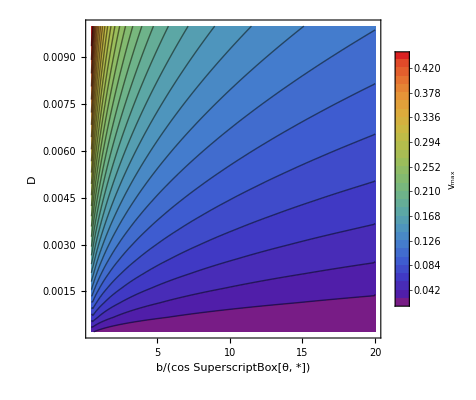
-Graphics-(A)

```mathematica
maxvelplot=ListContourPlot[Flatten[Transpose[vpoints2],1],
FrameLabel->{{Style[HoldForm[D],24,Black],None},{Style[HoldForm["b/(cos SuperscriptBox[θ, *])"],24,Black],None}},
BaselinePosition->Axis,AxesOrigin->{0,0.0045},
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize-> 24,Black},LegendFunction->fixLegend[310],
LegendLabel->Placed[Style["v_max",24,Black],Right,Rotate[#,-90 Degree] &]],After],
ColorFunction->"Rainbow",
FrameTicksStyle->Directive[FontSize->24,Black],
ImageSize->Automatic->300,
PlotRange->All,
ClippingStyle->None,
Contours->30];
maxvelfig=stripGridAlignment@Labeled[maxvelplot,{Style["(A)",24,Black]},{{Top, Left}}]
```

```mathematica
vpoints2[[40]];
```

```mathematica
3. max v for different values of r/b, SuperStar[θ], D
```

```mathematica
ratvals=bvals;
Dvals;
fixedD = 0.002;
thetavals = Table[t,{t,(3*π)/8,π/8,-π/8}];
rvals = {1,2,3,4,5};
stable2 = Table[Cos[thetavals[[thetaind]]]/(ratvals[[ratind]]*rvals[[rind]]),{ratind, 1, Length[ratvals]},{rind,1,Length[rvals]},{thetaind,1,Length[thetavals]}];
```

```mathematica
solutionsratvplots=Table[NSolve[{v==NI/(Nh*stable2[[ratind,rind,thetaind]]),v==fixedD^(2/3)*stable2[[ratind,rind,thetaind]]^(1/3)*(24*Log[NI*(fixedD*stable2[[ratind,rind,thetaind]]^2)^(1/3)])^(1/3)},{v,NI},Reals],{ratind, 1, Length[ratvals]},{rind,1,Length[rvals]},{thetaind,1,Length[thetavals]}];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

```mathematica
Dimensions[solutionsratvplots];
```

```mathematica
vbetaoverrpoints = Table[
{1/(rvals[[rind]]*stable2[[ratind,rind,thetaind]]/Cos[thetavals[[thetaind]]]),v/.solutionsratvplots[[ratind,rind,thetaind,2]]},{ratind, 1, Length[ratvals]},{rind,1,Length[rvals]},{thetaind,1,Length[thetavals]}];
```

```mathematica
vratplotspointsall= Table[
{1/(rvals[[rind]]*stable2[[ratind,rind,thetaind]]/Cos[thetavals[[thetaind]]]),(rvals[[rind]]/v)/.solutionsratvplots[[ratind,rind,thetaind,2]]},{ratind, 1, Length[ratvals],1},{rind,1,Length[rvals]},{thetaind,1,Length[thetavals]}]; (*for use in tmrca calculation*)
```

```mathematica
vratplotspoints = Table[
{1/(rvals[[rind]]*stable2[[ratind,rind,thetaind]]/Cos[thetavals[[thetaind]]]),(rvals[[rind]]/v)/.solutionsratvplots[[ratind,rind,thetaind,2]]},{ratind, 1, Length[ratvals],5},{rind,1,Length[rvals]},{thetaind,1,Length[thetavals]}];
```

```mathematica
transposepoints=TensorTranspose[vratplotspoints,{3,2,1,4}];
```

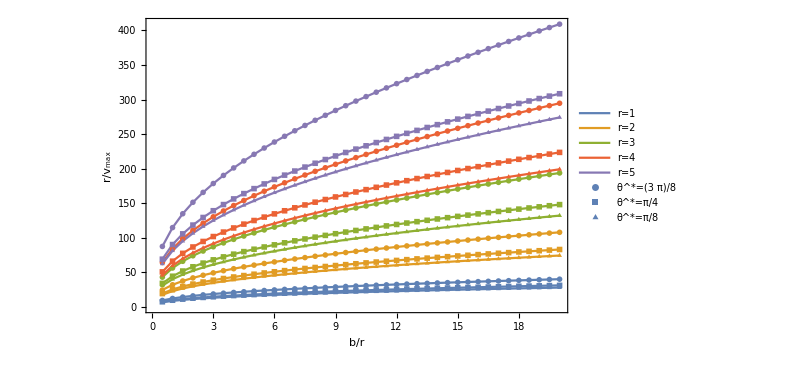

```mathematica
rlines1=ListPlot[transposepoints[[1]],PlotRange->All,LabelStyle->Directive[Black,FontSize->24], Joined->True, PlotLegends->{"r=1","r=2","r=3","r=4","r=5"}, PlotStyle->{Thick,"Rainbow"}];
rlines2=ListPlot[transposepoints[[2]],PlotRange->All,LabelStyle->Directive[Black,FontSize->24], Joined->True, PlotLegends->None, PlotStyle->{Thick,"Rainbow"}];
rlines3=ListPlot[transposepoints[[3]],PlotRange->All,LabelStyle->Directive[Black,FontSize->24], Joined->True, PlotLegends->None, PlotStyle->{Thick,"Rainbow"}];
theta1points = ListPlot[transposepoints[[1]],PlotRange->All, Joined->False, PlotLegends->{"θ^*=(3  π)/8"},PlotStyle->Directive[{PointSize[Medium],"Rainbow"}],PlotMarkers->{•,20},LabelStyle->Directive[Black,FontSize->24]];
theta2points = ListPlot[transposepoints[[2]],PlotRange->All, Joined->False, PlotLegends->{"θ^*=π/4"}, PlotStyle->Directive[{PointSize[Medium],"Rainbow"}],PlotMarkers->{■,20},LabelStyle->Directive[Black,FontSize->24]];
theta3points = ListPlot[transposepoints[[3]],PlotRange->All,Joined->False, PlotLegends->{"θ^*=π/8"}, PlotStyle->Directive[{PointSize[Medium],"Rainbow"}],PlotMarkers->{▲,20},LabelStyle->Directive[Black,FontSize->24]];
rovervmaxplot=Show[rlines1,rlines2,rlines3,theta1points,theta2points,theta3points,
Frame->{True,True,False,False},
FrameLabel->{"b/r","r/v_max",None,None},
LabelStyle->Directive[FontSize->24,Black],
ImageSize->600];
rovervmaxfig=stripGridAlignment@Labeled[rovervmaxplot,{Style["",24,Black]},{{Top, Left}}]
```

```mathematica
vplotsmain = GraphicsRow[{maxvelfig,rovervmaxfig},ImageSize->1400]
```

-Graphics-

```mathematica
σ plots
```

### σ monotonically decreasing as a function of s

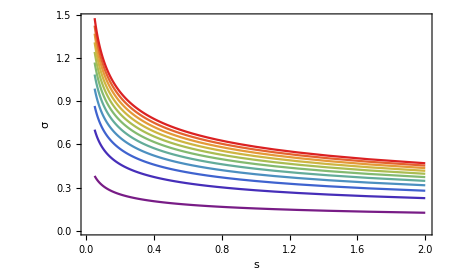

```mathematica
sigpoints = Table[{stable[[sind]],Sqrt[(vtable[[sind]][[Dind]][[2]])/stable[[sind]]]},{sind,1,Length[stable]},{Dind, 1, Length[Dvals],2}];
unjoinedsigplot = ListPlot[Transpose[sigpoints], Joined->False, PlotRange->All,AxesLabel->{"s","σ"}];
joinedsigplot = ListPlot[Transpose[sigpoints], 
Joined->True, 
FrameLabel->{"s","σ",None,None}, 
PlotRange->All, 
Frame->{True,True,False,False},
FrameStyle->{Black},
LabelStyle->{FontSize->24,Black},
PlotStyle->ColorData["Rainbow"][[1]],
ImageSize->450]
```

### sigma heatmap

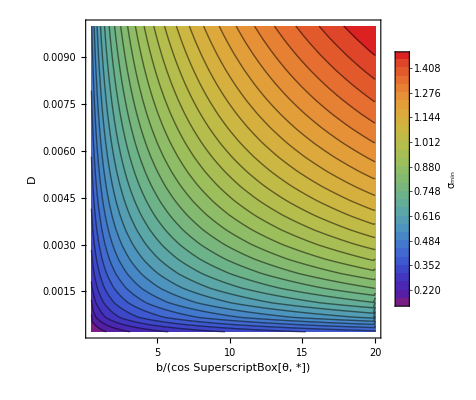
-Graphics-(B)

```mathematica
sigmintab = Table[{1/stable[[sind]],sigpoints2[[sind]][[Dind]][[2]]},{sind,1,Length[stable]},{Dind, 1, Length[Dvals],1}];
sigpointshm= Table[{bvals[[i]],Dvals[[Dind]],sigpoints2[[i]][[Dind]][[2]]},{i,1,Length[stable]},{Dind, 1, Length[Dvals], 1 }];

minsigplot=ListContourPlot[Flatten[Transpose[sigpointshm],1],
FrameLabel->{{Style[HoldForm[D],24,Black],None},{Style[HoldForm["b/(cos SuperscriptBox[θ, *])"],24,Black],None}},
BaselinePosition->Axis,AxesOrigin->{0,0.0045},
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize-> 24,Black},LegendFunction->fixLegend[310],
LegendLabel->Placed[Style["σ_min",24,Black],Right,Rotate[#,-90 Degree] &]],After],
ColorFunction->"Rainbow",
FrameTicksStyle->Directive[FontSize->24,Black],
ImageSize->Automatic->300,
Contours->30,
PlotRange->All];
minsigfig=stripGridAlignment@Labeled[minsigplot,{Style["(B)",24,Black]},{{Top, Left}}]
```

### sigma vs b/r

```mathematica
ClearAll[transposepoints]
```

```mathematica
sigbetaoverrpoints = Table[
{1/(rvals[[rind]]*stable2[[ratind,rind,thetaind]]/Cos[thetavals[[thetaind]]]),Sqrt[vbetaoverrpoints[[ratind,rind,thetaind,2]]/stable2[[ratind,rind,thetaind]]]},{ratind, 1, Length[ratvals]},{rind,1,Length[rvals]},{thetaind,1,Length[thetavals]}];
```

```mathematica
sigratplotspoints = Table[
{1/(rvals[[rind]]*stable2[[ratind,rind,thetaind]]/Cos[thetavals[[thetaind]]]),((1/rvals[[rind]])*Sqrt[v/stable2[[ratind,rind,thetaind]]])/.solutionsratvplots[[ratind,rind,thetaind,2]]},{ratind, 1, Length[ratvals],5},{rind,1,Length[rvals]},{thetaind,1,Length[thetavals]}];
```

```mathematica
transposepoints=TensorTranspose[sigratplotspoints,{3,2,1,4}];
```

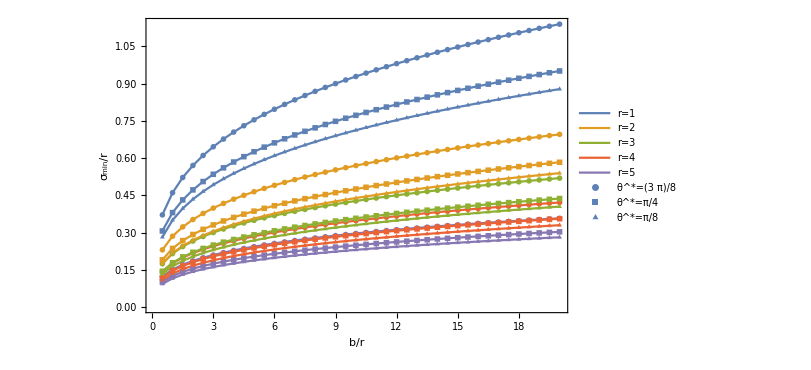

```mathematica
rlines1=ListPlot[transposepoints[[1]],PlotRange->All,LabelStyle->Directive[Black,FontSize->24], Joined->True, PlotLegends->{"r=1","r=2","r=3","r=4","r=5"}, PlotStyle->{Thick,"Rainbow"}];
rlines2=ListPlot[transposepoints[[2]],PlotRange->All,LabelStyle->Directive[Black,FontSize->24], Joined->True, PlotLegends->None, PlotStyle->{Thick,"Rainbow"}];
rlines3=ListPlot[transposepoints[[3]],PlotRange->All,LabelStyle->Directive[Black,FontSize->24], Joined->True, PlotLegends->None, PlotStyle->{Thick,"Rainbow"}];
theta1points = ListPlot[transposepoints[[1]],PlotRange->All, Joined->False, PlotLegends->{"θ^*=(3  π)/8"},PlotMarkers->{●,20},LabelStyle->Directive[Black,FontSize->24]];
theta2points = ListPlot[transposepoints[[2]],PlotRange->All, Joined->False, PlotLegends->{"θ^*=π/4"},PlotMarkers->{■,20},LabelStyle->Directive[Black,FontSize->24]];
theta3points = ListPlot[transposepoints[[3]],PlotRange->All,Joined->False, PlotLegends->{"θ^*=π/8"},PlotMarkers->{▲,20},LabelStyle->Directive[Black,FontSize->24]];
sigminoverrplot=Show[rlines1,rlines2,rlines3,theta1points,theta2points,theta3points,
Frame->{True,True,False,False},
FrameLabel->{"b/r","σ_min/r ",None,None},
LabelStyle->Directive[FontSize->24,Black],
ImageSize->600];
sigminoverrfig=stripGridAlignment@Labeled[sigminoverrplot,{Style["",24,Black]},{{Top, Left}}]
```

```mathematica
sigplotsmain = GraphicsRow[{minsigfig,sigminoverrfig},ImageSize->1400]
```

-Graphics-

## tmrca plots

### t_MRCA monotonically decreasing as a function of s

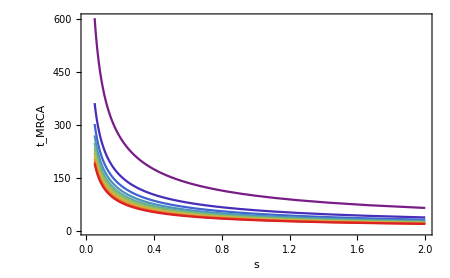

```mathematica
tmrcapoints = Table[{stable[[sind]],(α*(sigpoints2[[sind]][[Dind]][[2]])^2)/(2*Dvals[[Dind]])},{sind,1,Length[stable]},{Dind, 1, Length[Dvals],2}];
unjoinedtmrcaplot = ListPlot[Transpose[tmrcapoints], Joined->False, AxesLabel->{"s","σ"}, PlotRange->All];
joinedtmrcaplot = ListPlot[Transpose[tmrcapoints], 
Joined->True, 
FrameLabel->{"s","t_MRCA",None,None}, 
PlotRange->All, 
Frame->{True,True,False,False},
FrameStyle->{Black},
LabelStyle->{FontSize->24,Black},
PlotStyle->ColorData["Rainbow"][[1]],
ImageSize->450]
```

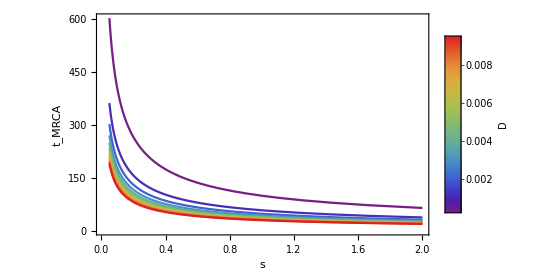

```mathematica
monotoniclegend = BarLegend[{"Rainbow",{0.0002,0.0095}},LabelStyle->{FontSize-> 24,Black},
LegendFunction->fixLegend[200],
LegendLabel->Placed[Style["D",24,Black],Right,Rotate[#,-90 Degree] &]];
joinedtmrcafig = Legended[joinedtmrcaplot,monotoniclegend]
```

```mathematica
tmrca heatmap
```

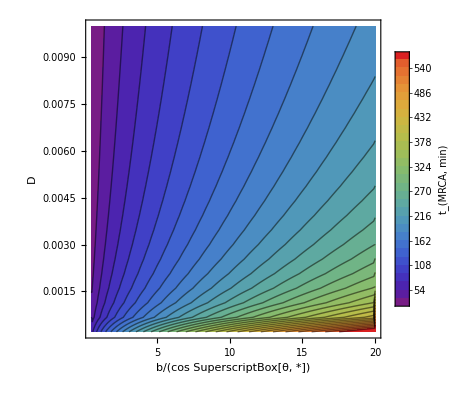
-Graphics-(C)

```mathematica
tmrcamintab = Table[{1/stable[[sind]],tmrcapoints2[[sind]][[Dind]][[2]]},{sind,1,Length[stable]},{Dind, 1, Length[Dvals],1}];
tmrcapointshm= Table[{bvals[[i]],Dvals[[Dind]],tmrcamintab[[i]][[Dind]][[2]]},{i,1,Length[stable]},{Dind, 1, Length[Dvals], 1 }];

mintmrcaplot=ListContourPlot[Flatten[Transpose[tmrcapointshm],1],
FrameLabel->{{Style[HoldForm[D],24,Black],None},{Style[HoldForm["b/(cos SuperscriptBox[θ, *])"],24,Black],None}},
BaselinePosition->Axis,AxesOrigin->{0,0.0045},
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize-> 24,Black},LegendFunction->fixLegend[310],
LegendLabel->Placed[Style["t_(MRCA,  min)",24,Black],Right,Rotate[#,-90 Degree] &]],After],
ColorFunction->"Rainbow",
FrameTicksStyle->Directive[FontSize->24,Black],
ImageSize->Automatic->300,
Contours->30,
PlotRange->All];
mintmrcafig=stripGridAlignment@Labeled[mintmrcaplot,{Style["(C)",24,Black]},{{Top, Left}}]
```

```mathematica
ClearAll[transposepoints]
```

```mathematica
tmrcabetaoverrpoints = Table[
{1/(rvals[[rind]]*stable2[[ratind,rind,thetaind]]/Cos[thetavals[[thetaind]]]),((α*sigbetaoverrpoints[[ratind,rind,thetaind,2]]^2)/(2*fixedD))},{ratind, 1, Length[ratvals]},{rind,1,Length[rvals]},{thetaind,1,Length[thetavals]}];
```

```mathematica
tmrcaratplotspoints = Table[
{1/(rvals[[rind]]*stable2[[ratind,rind,thetaind]]/Cos[thetavals[[thetaind]]]),((α*sigbetaoverrpoints[[ratind,rind,thetaind,2]]^2)/(2*fixedD))},{ratind, 1, Length[ratvals],5},{rind,1,Length[rvals]},{thetaind,1,Length[thetavals]}];
```

```mathematica
vbetaoverrpoints[[3,3,3]]
```

{0.7,0.0855493}

```mathematica
sigbetaoverrpoints[[3,3,3]]
```

{0.7,0.440971}

```mathematica
Dimensions[tmrcaratplotspoints]
```

{40,5,3,2}

```mathematica
tmrcabetaoverrpoints[[3,3,3]]
```

{0.7,80.699}

```mathematica
transposepoints=TensorTranspose[tmrcaratplotspoints,{3,2,1,4}];
```

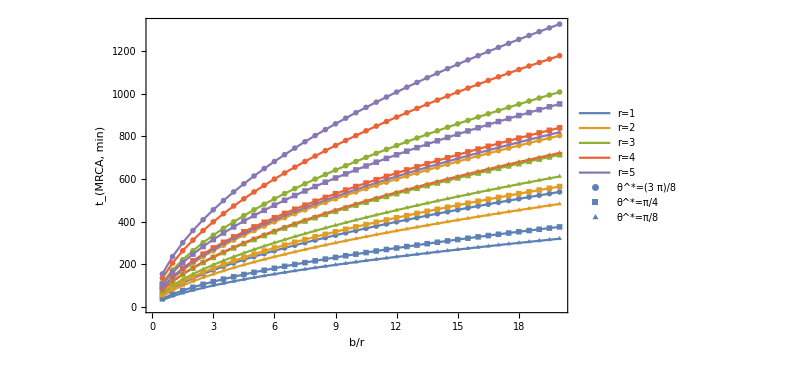

```mathematica
rlines1=ListPlot[transposepoints[[1]],PlotRange->All,LabelStyle->Directive[Black,FontSize->24], Joined->True, PlotLegends->{"r=1","r=2","r=3","r=4","r=5"}, PlotStyle->{Thick,"Rainbow"}];
rlines2=ListPlot[transposepoints[[2]],PlotRange->All,LabelStyle->Directive[Black,FontSize->24], Joined->True, PlotLegends->None, PlotStyle->{Thick,"Rainbow"}];
rlines3=ListPlot[transposepoints[[3]],PlotRange->All,LabelStyle->Directive[Black,FontSize->24], Joined->True, PlotLegends->None, PlotStyle->{Thick,"Rainbow"}];
theta1points = ListPlot[transposepoints[[1]],PlotRange->All, Joined->False, PlotLegends->{"θ^*=(3  π)/8"},PlotStyle->Directive[{PointSize[Medium],"Rainbow"}],PlotMarkers->●,LabelStyle->Directive[Black,FontSize->24]];
theta2points = ListPlot[transposepoints[[2]],PlotRange->All, Joined->False, PlotLegends->{"θ^*=π/4"}, PlotStyle->Directive[{PointSize[Medium],"Rainbow"}],PlotMarkers->■,LabelStyle->Directive[Black,FontSize->24]];
theta3points = ListPlot[transposepoints[[3]],PlotRange->All,Joined->False, PlotLegends->{"θ^*=π/8"}, PlotStyle->Directive[{PointSize[Medium],"Rainbow"}],PlotMarkers->▲,LabelStyle->Directive[Black,FontSize->24]];
tmrcaminoverrplot=Show[rlines1,rlines2,rlines3,
theta1points,theta2points,theta3points,
Frame->{True,True,False,False},
FrameLabel->{"b/r","t_(MRCA, min) ",None,None},
LabelStyle->Directive[FontSize->24,Black],
ImageSize->600];
tmrcaminoverrfig=stripGridAlignment@Labeled[tmrcaminoverrplot,{Style["",24,Black]},{{Top, Left}}]
```

```mathematica
tmrcaplotsmain = GraphicsRow[{mintmrcafig,tmrcaminoverrfig},ImageSize->1400]
```

-Graphics-

```mathematica
dynamicsfig = GraphicsColumn[{vplotsmain,sigplotsmain,tmrcaplotsmain},ImageSize->1500]
```

-Graphics-

```mathematica
monotonicvfig = Labeled[joinedvplot,{Style["(A)",24,Black]},{{Top, Left}}];
monotonicsigfig = Labeled[joinedsigplot,{Style["(B)",24,Black]},{{Top, Left}}];
monotonictmrcafig = Labeled[joinedtmrcafig,{Style["(C)",24,Black]},{{Top, Left}}];
```

```mathematica
methodsfig = GraphicsRow[{monotonicvfig,monotonicsigfig,monotonictmrcafig},ImageSize->1800]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../figures/dynamics.pdf",dynamicsfig]
Export["../figures/monotonic.pdf",methodsfig]
```